# ππ Global Fits (Phys.Rev.D 111, 074003 (2025))

## General Definitions

```mathematica
physval={Mp->0.13957,Mk->0.4957,Me->0.54751,Mω->0.78266};
```

```mathematica
w[s_,s0_]=(√s-√(s0-s))/(√s+√(s0-s));
kp[s_]=√(s/4-Mp^2);
kk[s_]=√(s/4-Mk^2);
k2[s_]=Abs[kk[s]];
ke[s_]=√(s/4-Me^2);
σp[s_]=√(1-(4 Mp^2)/s);
σk[s_]=√(1-(4 Mk^2)/s);
σpp[s_]=Piecewise[{{σp[s],Im[s]>=0},{-σp[s],Im[s]<0}}];
σkk[s_]=Piecewise[{{σk[s],Im[s]>=0},{-σk[s],Im[s]<0}}];
chev1[s_]=s;
chev2[s_]=2 s^2-1;
chev3[s_]=4 s^3-3 s;
chev4[s_]=8 s^4-8 s^2+1;
chev5[s_]=16 s^5-20 s^3+5 s;
chev6[s_]=32 s^6-48 s^4+18 s^2-1;
chev7[s_]=64 s^7-112 s^5+56 s^3-7 s;
```

## S0 wave (given in Eur.Phys.J.C 79, 1008 (2019), see also the erratum)

#### Parameters

```mathematica
S0par1={B000->11.4,B100->-0.6,B200->18.6,B300->-6.7,B400->-20.2,B500->5.6,rsp00->0.996,isp00->0.025,k000->5.04,k100->-4.36,k200->-0.05,k300->-0.28,d000->-11.9,d100->0,d200->0,ϵ200->13.7,ϵ300->0,ϵ400->0,z00->0.137};

ΔS0par1={ΔB000->0.3,ΔB100->1.1,ΔB200->2.7,ΔB300->3.1,ΔB400->3.7,ΔB500->4.8,Δrsp00->0,Δisp00->0,Δk000->0.28,Δk100->0.16,Δk200->0.16,Δk300->0.06,Δd000->3.7,Δd100->0,Δd200->0,Δϵ200->4.0,Δϵ300->0,Δϵ400->0,Δz00->0.028};

S0par2={B000->12.1,B100->-1.4,B200->14.8,B300->-4.9,B400->-18.9,B500->0.5,rsp00->0.996,isp00->0.025,k000->5.02,k100->-4.71,k200->0.01,k300->-0.36,d000->-11.1,d100->0,d200->0,ϵ200->81.7,ϵ300->-183.8,ϵ400->-51,z00->0.137};

ΔS0par2={ΔB000->0.3,ΔB100->0.8,ΔB200->1.5,ΔB300->1.5,ΔB400->1.3,ΔB500->4.5,Δrsp00->0,Δisp00->0,Δk000->0.08,Δk100->0.08,Δk200->0.18,Δk300->0.04,Δd000->6.2,Δd100->0,Δd200->0,Δϵ200->2.4,Δϵ300->8.5,Δϵ400->25,Δz00->0.028};

S0par3={B000->11.9,B100->-1.0,B200->16.5,B300->-5.3,B400->-22.7,B500->5.6,rsp00->0.996,isp00->0.025,k000->5.28,k100->-4.64,k200->0.18,k300->-0.37,d000->73.3,d100->27.4,d200->-0.27,ϵ200->171.7,ϵ300->-1041,ϵ400->1678,z00->0.137};

ΔS0par3={ΔB000->0.3,ΔB100->0.9,ΔB200->1.7,ΔB300->1.6,ΔB400->1.2,ΔB500->2.8,Δrsp00->0,Δisp00->0,Δk000->0.08,Δk100->0.04,Δk200->0.07,Δk300->0.04,Δd000->1.5,Δd100->0.4,Δd200->0.2,Δϵ200->2,Δϵ300->8,Δϵ400->31,Δz00->0.028};
```

#### Amplitude below 1.4 GeV

First, we define the conformal amplitude

```mathematica
s000=4 Mk^2;
```

```mathematica
sp00=(rsp00-I isp00)^2;
```

```mathematica
v00[s_]=w[s+ I 10^-18,s000];
```

```mathematica
cotδ00conf[s_]=s^(1/2)/(2 kp[s])Mp^2/(s-z00^2/2)(z00^2/(Mp s^(1/2))+B000+B100 v00[s]+B200 v00[s]^2+B300 v00[s]^3+B400 v00[s]^4+B500 v00[s]^5);
```

```mathematica
t00conf[s_]=1/(σpp[s] (cotδ00conf[s]- I));
```

Now, we implement the f0(980) amplitude

```mathematica
Jp00[s_]=2/Pi+σpp[s]/Pi*Log[(σpp[s]-1)/(σpp[s]+1)];
Jk00[s_]=2/Pi+σkk[s]/Pi*Log[(σkk[s]-1)/(σkk[s]+1)];
vchev00[s_]=2 (s^(1/2)-2 Mk)/(1.5-2 Mk)-1;
```

```mathematica
f00[s_]=Mk^2 (k000+k100 chev1[vchev00[s]]+k200 chev2[vchev00[s]]+k300 chev3[vchev00[s]]);
fr=Re[f00[sp00]];
fi=Im[f00[sp00]];
Jkr=Re[Jk00[sp00]];
Jki=Im[Jk00[sp00]];
Jpr=Re[Jp00[sp00]];
Jpi=Im[Jp00[sp00]];
sigmar=Re[σpp[sp00]];
sigmai=Im[σpp[sp00]];
sr=Re[sp00];
si=Im[sp00];
d=Jpi sr+Jpr si+2*(sigmai si-sigmar sr);
G=-(fi Jkr+fr Jki+si)/d;
M=((fi Jkr+fr Jki)*(si*(Jpi-2 sigmar)-sr*(Jpr+2 sigmai))+(Jpi-2 sigmar)*(si^2+sr^2))/d-(fi Jki-fr Jkr);
```

```mathematica
t00f[s_]:=(s*G)/(M-s-Jp00[s]*s*G-Jk00[s]*f00[s]);
```

Let’s define the total amplitude below 1.4 GeV

```mathematica
tlow00[s_]=t00conf[s]+t00f[s]+2 I σpp[s] t00conf[s] t00f[s];
```

```mathematica
Slow00[s_]=1+2 I σpp[s] tlow00[s];
```

```mathematica
δlow00[s_]:=Piecewise[{{1/2 ArcTan[Re[Slow00[s]],Im[Slow00[s]]],Im[Slow00[s]]>=0&&s<=0.9^2},{1/2 ArcTan[Re[Slow00[s]],Im[Slow00[s]]]+π,Im[Slow00[s]]<0&&s<=1.2^2},{1/2 ArcTan[Re[Slow00[s]],Im[Slow00[s]]]+π,Im[Slow00[s]]>=0&&s>0.9^2},{1/2 ArcTan[Re[Slow00[s]],Im[Slow00[s]]]+2π,Im[Slow00[s]]<0&&s>1.2^2}}]180/π
```

```mathematica
ηlow00[s_]=Abs[Slow00[s]];
```

#### Amplitude above 1.4 GeV

We start with the phase-shift

```mathematica
sm00=1.4^2;
```

```mathematica
vchev200[s_]=2 (s^(1/2)-sm00^(1/2))/(2-sm00^(1/2))-1;
```

```mathematica
derδ00=(δlow00[sm00+10^-5]-δlow00[sm00-10^-5])/(2 10^-5);
derη00=(ηlow00[sm00+10^-5]-ηlow00[sm00-10^-5])/(2 10^-5);
derv00=(vchev200[sm00+10^-5]-vchev200[sm00-10^-5])/(2 10^-5);
```

```mathematica
Δ00=derδ00/derv00+4 d000-9d100+16d200;
```

```mathematica
δhigh00[s_]:=δlow00[sm00]+ Δ00 (chev1[vchev200[s]]+1)+ d000 (chev2[vchev200[s]]-1)+ d100 (chev3[vchev200[s]]+1)+ d200 (chev4[vchev200[s]]-1);
```

Finally, we define the elasticity above 1.4 GeV

```mathematica
qm00=kp[sm00];
Q00[s_]=kp[s]/qm00-1;
ϵ000=√(-Log[ηlow00[sm00]]);
ϵ100=(-4 qm00^2 derη00)/(ϵ000 ηlow00[sm00]);
```

```mathematica
ηhigh00[s_]=Exp[-(ϵ000+ϵ100 Q00[s]+ϵ200 Q00[s]^2+ϵ300 Q00[s]^3+ϵ400 Q00[s]^4)^2];
```

This is the final S0 Global Fit parametrization, and the corresponding phase-shift and elasticity functions

```mathematica
δ00[s_]:=Piecewise[{{δlow00[s],s<=sm00},{δhigh00[s],s>sm00}}];
η00[s_]=Piecewise[{{ηlow00[s],s<=sm00},{ηhigh00[s],s>sm00}}];
t00[s_]:=(η00[s] Exp[ⅈ δ00[s] π/90]-1)/(2ⅈ σpp[s]);
```

#### Plots

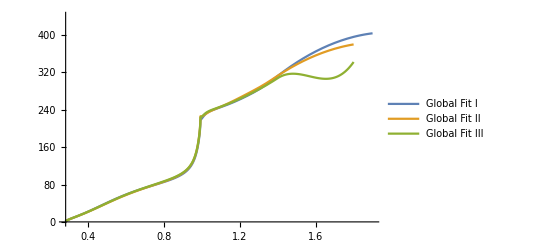

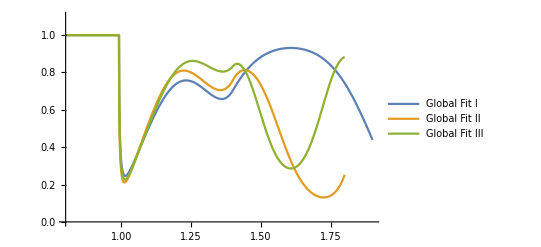

```mathematica
Plot[{δ00[e^2]/.S0par1/.physval,ConditionalExpression[δ00[e^2]/.S0par2/.physval,e<1.8],ConditionalExpression[δ00[e^2]/.S0par3/.physval,e<1.8]},{e,0.28,1.9},PlotRange->{0,440},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[{η00[e^2]/.S0par1/.physval,ConditionalExpression[η00[e^2]/.S0par2/.physval,e<1.8],ConditionalExpression[η00[e^2]/.S0par3/.physval,e<1.8]},{e,0.8,1.9},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## P wave

#### Parameters

```mathematica
Ppar1={B011->1.11,B111->-0.833,B211->0.80,B311->2.74,B411->-1.82,K011->0.396,K111->-0.5825,K211->0.2616,K311->-0.0120,mρ->0.7707,d211->-64.64,d311->-46.95,d411->-31.14,d511->-10.82,d611->-0.928,ϵ211->-0.026,ϵ311->0.321,ϵ411->0.131};

ΔPpar1={ΔB011->0.05,ΔB111->0.013,ΔB211->0.04,ΔB311->0.08,ΔB411->0.10,ΔK011->0.003,ΔK111->0.0008,ΔK211->0.0005,ΔK311->0.0003,Δmρ->0.0012,Δd211->0.26,Δd311->0.08,Δd411->0.04,Δd511->0.03,Δd611->0.018,Δϵ211->0.009,Δϵ311->0.004,Δϵ411->0.003};

Ppar2={B011->1.20,B111->-1.193,B211->1.47,B311->3.17,B411->-2.71,K011->0.4475,K111->-0.6936,K211->0.3529,K311->-0.0459,mρ->0.7697,d211->0.3,d311->0.61,d411->0,d511->0,d611->0,ϵ211->-0.19,ϵ311->-0.024,ϵ411->0.0033};

ΔPpar2={ΔB011->0.06,ΔB111->0.016,ΔB211->0.05,ΔB311->0.09,ΔB411->0.11,ΔK011->0.0015,ΔK111->0.0008,ΔK211->0.0005,ΔK311->0.0003,Δmρ->0.0012,Δd211->0.4,Δd311->0.10,Δd411->0,Δd511->0,Δd611->0,Δϵ211->0.012,Δϵ311->0.003,Δϵ411->0.0016};

Ppar3={B011->1.18,B111->-1.144,B211->1.30,B311->3.26,B411->-2.72,K011->0.4638,K111->-0.6850,K211->0.3151,K311->-0.0223,mρ->0.7696,d211->0.6,d311->0.22,d411->0,d511->0,d611->0,ϵ211->-0.282,ϵ311->-0.067,ϵ411->-0.0171};

ΔPpar3={ΔB011->0.06,ΔB111->0.017,ΔB211->0.05,ΔB311->0.10,ΔB411->0.14,ΔK011->0.0019,ΔK111->0.0011,ΔK211->0.0007,ΔK311->0.0005,Δmρ->0.0012,Δd211->0.5,Δd311->0.13,Δd411->0,Δd511->0,Δd611->0,Δϵ211->0.013,Δϵ311->0.004,Δϵ411->0.0018};
```

#### Amplitude below 1.4 GeV

First, we define the conformal amplitude

```mathematica
s011=1.43^2;
α11=0.3;
sm11=(Mp+Mω)^2;
```

```mathematica
w11[s_]=(√s-α11 √(s011-s))/(√s+α11 √(s011-s));
v11[s_]=w11[s+ 10^-18 I];
```

```mathematica
cotδ11conf[s_]=(mρ^2-s)/(σpp[s] kp[s]^2) ((2 Mp^3)/(mρ^2 s^(1/2))+B011+B111 v11[s]+B211 v11[s]^2+B311 v11[s]^3+B411 v11[s]^4);
```

```mathematica
t11conf[s_]=1/(σpp[s] (cotδ11conf[s]- I));
```

```mathematica
S11conf[s_]=1+2 I σpp[s] t11conf[s];
```

Now, we implement the inelastic amplitude

```mathematica
ν[s_]=√((s-(Mp+Mω)^2) (s-(Mp-Mω)^2));
```

```mathematica
ΔJ=Mp^2-Mω^2;
ΣJ=Mp^2+Mω^2;
```

```mathematica
J11[s_]=(2+(ΔJ/s-ΣJ/ΔJ) Log[Mω^2/Mp^2]+ν[s]/s (Log[(ν[s]-s+ΔJ)/(ν[s]+s+ΔJ)]+Log[(ν[s]-s-ΔJ)/(ν[s]+s-ΔJ)]))/(2 π);
```

```mathematica
Mprom=Mp+Mω;
k2πω[s_]=ν[s]^2/(4 s);
R11[s_]=s/Mprom^2-1;
```

```mathematica
δ11in[s_]:=J11[s] (K011+K111 R11[s]+K211 R11[s]^2+K311 R11[s]^3) k2πω[s]/Mprom^2 kp[s]^3/(Mp^2 s^(1/2));
```

```mathematica
t11in[s_]:=(Exp[2ⅈ δ11in[s]]-1)/(2ⅈ σp[s]);
```

```mathematica
S11in[s_]:=Exp[2ⅈ δ11in[s]];
```

Let’s define the total amplitude below 1.4 GeV

```mathematica
Slow11[s_]:=S11conf[s] S11in[s];
```

```mathematica
δlow11[s_]:=Piecewise[{{1/2 ArcTan[Re[Slow11[s]],Im[Slow11[s]]],Im[Slow11[s]]>=0},{1/2 ArcTan[Re[Slow11[s]],Im[Slow11[s]]]+π,Im[Slow11[s]]<0}}] 180/π;
```

```mathematica
ηlow11[s_]:=Abs[Slow11[s]];
```

#### Amplitude above 1.4 GeV

We start with the phase-shift

```mathematica
sm211=1.4^2;
```

```mathematica
vchev211[s_]=2 (s^(1/2)-sm211^(1/2))/(2-sm211^(1/2))-1;
```

```mathematica
derδ11=(δlow11[sm211+10^-5]-δlow11[sm211-10^-5])/(2 10^-5);
```

```mathematica
derη11=(ηlow11[sm211+10^-5]-ηlow11[sm211-10^-5])/(2 10^-5);
```

```mathematica
derv11=(vchev211[sm211+10^-5]-vchev211[sm211-10^-5])/(2 10^-5);
```

```mathematica
Δ11=derδ11/derv11+4 d211-9d311+16 d411-25d511+36 d611;
```

```mathematica
δhigh11[s_]:=δlow11[sm211]+ Δ11 (chev1[vchev211[s]]+1)+ d211 (chev2[vchev211[s]]-1)+ d311 (chev3[vchev211[s]]+1)+ d411 (chev4[vchev211[s]]-1)+ d511 (chev5[vchev211[s]]+1)+ d611 (chev6[vchev211[s]]-1);
```

Finally, we define the elasticity above 1.4 GeV

```mathematica
ϵ011=√(-Log[ηlow11[sm211]]); (* Caution,this eps0 is different from the one in the paper,everything is rewritten in a different way *)
```

```mathematica
ϵ111=-derη11/(2 ϵ011 ηlow11[sm211] derv11)+4 ϵ211-9ϵ311+16 ϵ411;
```

```mathematica
ηhigh11[s_]:=Exp[-(ϵ011+ϵ111 (chev1[vchev211[s]]+1)+ϵ211 (chev2[vchev211[s]]-1)+ϵ311 (chev3[vchev211[s]]+1)+ϵ411 (chev4[vchev211[s]]-1))^2];
```

This is the final P Global Fit parametrization, and the corresponding phase-shift and elasticity functions

```mathematica
δ11[s_]:=Piecewise[{{δlow11[s],s<=sm211},{δhigh11[s],s>sm211}}];
```

```mathematica
η11[s_]:=Piecewise[{{ηlow11[s],s<=sm211},{ηhigh11[s],s>sm211}}];
```

```mathematica
t11[s_]:=(η11[s]Exp[ⅈ δ11[s] π/90]-1)/(2ⅈ σpp[s]);
```

#### Plots

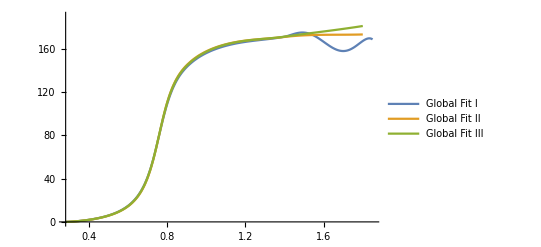

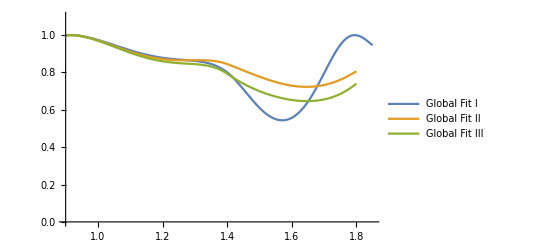

```mathematica
Plot[{δ11[e^2]/.Ppar1/.physval,ConditionalExpression[δ11[e^2]/.Ppar2/.physval,e<1.8],ConditionalExpression[δ11[e^2]/.Ppar3/.physval,e<1.8]},{e,0.28,1.85},PlotRange->{0,190},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[{η11[e^2]/.Ppar1/.physval,ConditionalExpression[η11[e^2]/.Ppar2/.physval,e<1.8],ConditionalExpression[η11[e^2]/.Ppar3/.physval,e<1.8]},{e,0.9,1.85},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## S2 wave

#### Parameters

```mathematica
S2par1={B020->-76.5,B120->-57,z20->0.142,Bh220->290,Bh320->-2466,ϵ20->0.32};

ΔS2par1={ΔB020->2.8,ΔB120->11,Δz20->0.004,ΔBh220->109,ΔBh320->355,Δϵ20->0.06};

S2par2={B020->-80.2,B120->-64,z20->0.147,Bh220->340,Bh320->-2489,ϵ20->0.33};

ΔS2par2={ΔB020->2.8,ΔB120->11,Δz20->0.004,ΔBh220->109,ΔBh320->355,Δϵ20->0.06};

S2par3={B020->-78.1,B120->-58,z20->0.145,Bh220->327,Bh320->-2615,ϵ20->0.30};

ΔS2par3={ΔB020->2.8,ΔB120->11,Δz20->0.004,ΔBh220->109,ΔBh320->355,Δϵ20->0.06};
```

#### Amplitude

First, we define the phase-shift, which has two conformal pieces

```mathematica
s020=1.05^2;
sh20=2.3^2;
sm20=0.85^2;
smη20=0.915^2;
```

```mathematica
v20[s_]=w[s+ I 10^-18,s020];
vh20[s_]=w[s+ I 10^-18,sh20];
```

```mathematica
cotδ20conf1[s_]=s^(1/2)/(2 kp[s])Mp^2/(s-2 z20^2)(B020+B120 v20[s]);
```

```mathematica
Bh020=B020+B120 v20[sm20];
Bh120=B120 s020/sh20 (√(sh20-sm20))/(√(s020-sm20))((√sm20+√(sh20-sm20))/(√sm20+√(s020-sm20)))^2;
```

```mathematica
cotδ20conf2[s_]=s^(1/2)/(2 kp[s])Mp^2/(s-2 z20^2)(Bh020+Bh120 (vh20[s]-vh20[sm20])+Bh220 (vh20[s]-vh20[sm20])^2+Bh320 (vh20[s]-vh20[sm20])^3);
```

The phase-shift is given by

```mathematica
δ20conf1[s_]=ArcCot[cotδ20conf1[s]];
δ20conf2[s_]=ArcCot[cotδ20conf2[s]];
```

```mathematica
δ20[s_]=Piecewise[{{δ20conf1[s],s<=sm20},{δ20conf2[s],s>sm20}}] 180/π;
```

Now we define the elasticity

```mathematica
η20[s_]=Piecewise[{{1,s<=smη20},{1-ϵ20(1-smη20/s)^1.5,s>smη20}}];
```

This is the final S2 Global Fit parametrization

```mathematica
t20[s_]=(η20[s]Exp[2ⅈ δ20[s] π/180]-1)/(2ⅈ σpp[s]);
```

#### Plots

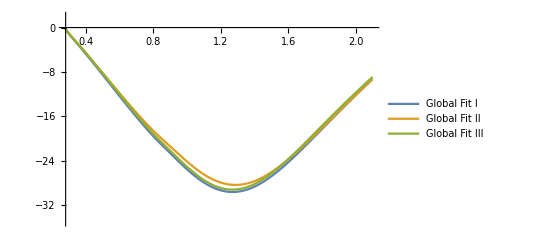

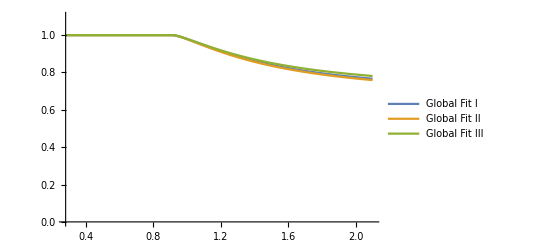

```mathematica
Plot[{δ20[e^2]/.S2par1/.physval,δ20[e^2]/.S2par2/.physval,δ20[e^2]/.S2par3/.physval},{e,0.28,2.1},PlotRange->{-35,2},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[{η20[e^2]/.S2par1/.physval,η20[e^2]/.S2par2/.physval,η20[e^2]/.S2par3/.physval},{e,0.28,2.1},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## D0 wave

#### Parameters

```mathematica
D0par1={B002->12.34,B102->10.12,Bh202->4.5,ϵ02->0.258,r02->0.94,Mf2->1.2746,d202->-12.18,d302->-1.94,d402->-3.01,ϵ202->0.22,ϵ302->3.71,ϵ402->-4.3,smη02->0.9^2};

ΔD0par1={ΔB002->0.13,ΔB102->0.15,ΔBh202->1.8,Δϵ02->0.015,Δr02->0.03,ΔMf2->0.0008,Δd202->0.17,Δd302->0.05,Δd402->0.03,Δϵ202->0.13,Δϵ302->0.22,Δϵ402->0.4,Δsmη02->0};

D0par2={B002->12.42,B102->10.00,Bh202->33,ϵ02->0.317,r02->1.10,Mf2->1.2756,d202->-39.7,d302->-19.28,d402->-8.86,ϵ202->11.99,ϵ302->-25.49,ϵ402->16.3,smη02->4 Mk^2};

ΔD0par2={ΔB002->0.13,ΔB102->0.15,ΔBh202->4,Δϵ02->0.026,Δr02->0.04,ΔMf2->0.0008,Δd202->0.5,Δd302->0.14,Δd402->0.07,Δϵ202->0.11,Δϵ302->0.23,Δϵ402->0.4,Δsmη02->0};

D0par3={B002->12.48,B102->10.02,Bh202->34,ϵ02->0.322,r02->1.16,Mf2->1.2754,d202->-82.4,d302->-42.65,d402->-14.38,ϵ202->10.20,ϵ302->-18.8,ϵ402->14.2,smη02->4 Mk^2};

ΔD0par3={ΔB002->0.13,ΔB102->0.15,ΔBh202->5,Δϵ02->0.024,Δr02->0.03,ΔMf2->0.0008,Δd202->0.5,Δd302->0.14,Δd402->0.07,Δϵ202->0.20,Δϵ302->0.4,Δϵ402->0.7,Δsmη02->0};
```

#### Amplitude below 1.4 GeV

First, we define the phase-shift, which has two conformal pieces

```mathematica
s002=1.05^2;
sh02=1.45^2;
sm02=4 Mk^2;
sm202=1.4^2;
```

```mathematica
v02[s_]=w[s+ I 10^-18,s002];
vh02[s_]=w[s+ I 10^-18,sh02];
```

```mathematica
cotδ02conf1[s_]=s^(1/2)/(2 kp[s]^5)(Mf2^2-s)Mp^2(B002+B102 v02[s]);
```

```mathematica
δ02conf1[s_]=ArcCot[cotδ02conf1[s]];
```

```mathematica
Bh102=B102 s002/sh02 (√(sh02-sm02))/(√(s002-sm02)) ((√sm02+√(sh02-sm02))/(√sm02+√(s002-sm02)))^2 - 2 Bh202 vh02[sm02];
Bh002=B002+B102 v02[sm02]-Bh102 vh02[sm02]-Bh202 vh02[sm02]^2;
```

```mathematica
cotδ02conf2[s_]=s^(1/2)/(2 kp[s]^5)(Mf2^2-s)Mp^2(Bh002+Bh102 vh02[s]+Bh202 vh02[s]^2);
```

The phase-shift below 1.4 GeV is given by

```mathematica
δ02conf2[s_]=ArcCot[cotδ02conf2[s]];
```

```mathematica
δlow02[s_]=Piecewise[{{δ02conf1[s],s<=sm02},{δ02conf2[s],sm02<s&&Re[δ02conf2[s]]>0},{δ02conf2[s]+π,sm02<s&&Re[δ02conf2[s]]<0}}]*180/π;
```

Now we define the elasticity below 1.4 GeV

```mathematica
ηlow02[s_]=Piecewise[{{1,s<=smη02},{1-ϵ02 ((1-smη02/s)/(1-smη02/Mf2^2))^(5/2)(1+r02(1-(s-smη02)/(Mf2^2-smη02))),s>smη02}}];
```

The total amplitude below 1.4 GeV is given by

```mathematica
tlow02[s_]=(ηlow02[s]Exp[2ⅈ δlow02[s]]-1)/(2ⅈ σpp[s]);
```

#### Amplitude above 1.4 GeV

We start with the phase-shift

```mathematica
vchev02[s_]=2 (s^(1/2)-sm202^(1/2))/(2-sm202^(1/2))-1;
```

```mathematica
derδ02=(δlow02[sm202+10^-5]-δlow02[sm202-10^-5])/(2 10^-5);
derη02=(ηlow02[sm202+10^-5]-ηlow02[sm202-10^-5])/(2 10^-5);
derv02=(vchev02[sm202+10^-5]-vchev02[sm202-10^-5])/(2 10^-5);
```

```mathematica
Δ02=derδ02/derv02+4 d202-9 d302+16 d402;
```

```mathematica
δhigh02[s_]=δlow02[sm202]+ Δ02 (chev1[vchev02[s]]+1)+ d202 (chev2[vchev02[s]]-1)+d302 (chev3[vchev02[s]]+1)+ d402 (chev4[vchev02[s]]-1);
```

Finally, we define the elasticity above 1.4 GeV

```mathematica
qm02=kp[sm202];
Q02[s_]=s/sm202-1;
ϵ002=√(-Log[ηlow02[sm202]]);
ϵ102=(-sm202 derη02)/(2 ϵ002 ηlow02[sm202]);
```

```mathematica
ηhigh02[s_]=Exp[-(ϵ002+ϵ102 Q02[s]+ϵ202 Q02[s]^2+ϵ302 Q02[s]^3+ϵ402 Q02[s]^4 )^2];
```

This is the final D0 Global Fit parametrization, and the corresponding phase-shift and elasticity functions

```mathematica
δ02[s_]=Piecewise[{{δlow02[s],s<=sm202},{δhigh02[s],s>sm202}}];
```

```mathematica
η02[s_]=Piecewise[{{ηlow02[s],s<=sm202},{ηhigh02[s],s>sm202}}];
```

```mathematica
t02[s_]=(η02[s]Exp[ⅈ δ02[s] π/90]-1)/(2ⅈ σpp[s]);
```

#### Plots

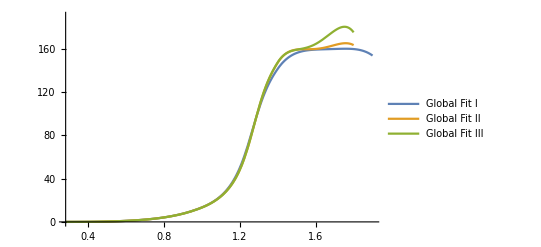

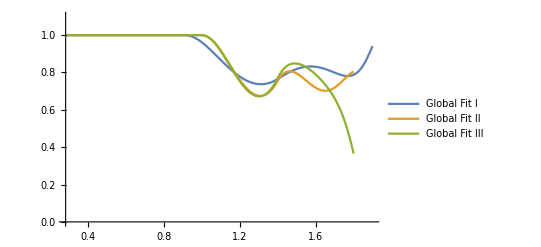

```mathematica
Plot[{δ02[e^2]/.D0par1/.physval,ConditionalExpression[δ02[e^2]/.D0par2/.physval,e<1.8],ConditionalExpression[δ02[e^2]/.D0par3/.physval,e<1.8]},{e,0.28,1.9},PlotRange->{0,190},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[{η02[e^2]/.D0par1/.physval,ConditionalExpression[η02[e^2]/.D0par2/.physval,e<1.8],ConditionalExpression[η02[e^2]/.D0par3/.physval,e<1.8]},{e,0.28,1.9},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## D2 wave

#### Parameters

```mathematica
D2par1={B022->4.6*10^3,B122->-1.4*10^3,B222->7*10^3,Bh222->83*10^3,Bh322->73*10^3,Δ22->0.235};

ΔD2par1={ΔB022->0.5*10^3,ΔB122->3.2*10^3,ΔB222->3*10^3,ΔBh222->13*10^3,ΔBh322->46*10^3,ΔΔ22->0.014};

D2par2={B022->4.4*10^3,B122->0.5*10^3,B222->10*10^3,Bh222->80*10^3,Bh322->110*10^3,Δ22->0.236};

ΔD2par2={ΔB022->0.5*10^3,ΔB122->3.2*10^3,ΔB222->3*10^3,ΔBh222->13*10^3,ΔBh322->46*10^3,ΔΔ22->0.014};

D2par3={B022->4.5*10^3,B122->-0.5*10^3,B222->10*10^3,Bh222->91*10^3,Bh322->80*10^3,Δ22->0.240};

ΔD2par3={ΔB022->0.5*10^3,ΔB122->3.2*10^3,ΔB222->3*10^3,ΔBh222->13*10^3,ΔBh322->46*10^3,ΔΔ22->0.014};
```

#### Amplitude

We define the phase-shift, which has two conformal pieces

```mathematica
s022=1.45^2;
sh22=2.4^2;
sm22=0.85^2;
v22[s_]=w[s+ I 10^-18,s022];
vh22[s_]=w[s+ I 10^-18,sh22];
```

```mathematica
cotδ22conf1[s_]=(s^(1/2) s Mp^4)/(2 kp[s]^5 (4*(Mp^2+ Δ22^2)-s))(B022+B122 v22[s]+B222 v22[s]^2);
```

```mathematica
Bh022=B022+B122 v22[sm22]+B222 v22[sm22]^2;
Bh122=(B122+2 B222 v22[sm22])s022/sh22 (√(sh22-sm22))/(√(s022-sm22))((√sm22+√(sh22-sm22))/(√sm22+√(s022-sm22)))^2;
```

```mathematica
cotδ22conf2[s_]=(s^(1/2) s Mp^4)/(2 kp[s]^5 (4(Mp^2+ Δ22^2)-s))(Bh022+Bh122 (vh22[s]-vh22[sm22])+Bh222 (vh22[s]-vh22[sm22])^2+Bh322 (vh22[s]-vh22[sm22])^3);
```

The phase-shift is given by

```mathematica
δ22conf1[s_]=ArcCot[cotδ22conf1[s]];
```

```mathematica
δ22conf2[s_]=ArcCot[cotδ22conf2[s]];
```

```mathematica
δ22[s_]=Piecewise[{{δ22conf1[s],s<=sm22},{δ22conf2[s],s>sm22}}] 180/π;
```

This is the final D2 Global Fit parametrization

```mathematica
t22[s_]=(Exp[2ⅈ δ22[s] π/180]-1)/(2ⅈ σpp[s]);
```

#### Plots

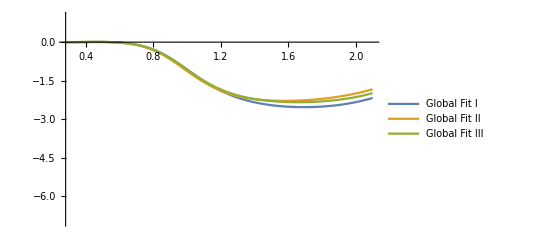

```mathematica
Plot[{δ22[e^2]/.D2par1/.physval,δ22[e^2]/.D2par2/.physval,δ22[e^2]/.D2par3/.physval},{e,0.28,2.1},PlotRange->{-7,1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## F wave

#### Parameters

```mathematica
Fpar1={b213->57.5*10^3,b313->-103*10^3,Γρ3->0.252,mρ3->1.711,Rρ3->5.06,xρ3->0.269};

ΔFpar1={Δb213->2.4*10^3,Δb313->6*10^3,ΔΓρ3->0.006,Δmρ3->0.002,ΔRρ3->0.02,Δxρ3->0.003};

Fpar2={b213->55.2*10^3,b313->-123*10^3,Γρ3->0.278,mρ3->1.724,Rρ3->4.92,xρ3->0.284};

ΔFpar2={Δb213->1.6*10^3,Δb313->8*10^3,ΔΓρ3->0.007,Δmρ3->0.002,ΔRρ3->0.02,Δxρ3->0.009};

Fpar3={b213->129.0*10^3,b313->10*10^3,Γρ3->0.242,mρ3->1.719,Rρ3->5.86,xρ3->0.235};

ΔFpar3={Δb213->1.6*10^3,Δb313->8*10^3,ΔΓρ3->0.005,Δmρ3->0.002,ΔRρ3->0.02,Δxρ3->0.002};
```

#### Amplitude

First, the Breit-Wigner amplitude, valid above 1.2 GeV

```mathematica
q13=kp[mρ3^2];
α13=0.5;
s013=1.5^2;
sm13=1.2^2;
sη13=(Mp+Mω)^2;
```

```mathematica
w13[s_]=(√s-α13 √(s013-s))/(√s+α13 √(s013-s));
v13[s_]=w13[s+ 10^-18 I];
Blatt3[s_]=s^6+6 s^4+45 s^2+225;
```

```mathematica
Γ13[s_]=Γρ3 (kp[s]/q13)^7 Blatt3[q13 Rρ3]/Blatt3[kp[s] Rρ3];
```

```mathematica
tbw13[s_]=(xρ3 mρ3 Γ13[s])/(σpp[s] (mρ3^2-s-I mρ3 Γ13[s]));
```

```mathematica
Sbw13[s_]=1+2 I σpp[s] tbw13[s];
```

```mathematica
δbw13[s_]=Re[ArcTan[Re[Sbw13[s]],Im[Sbw13[s]]] 90/π];
```

```mathematica
ηbw13[s_]=Abs[Sbw13[s]];
```

Now, let’s define the low-energy conformal amplitude, matched to the B-W amplitude at 1.2 GeV

```mathematica
fac13[s_]=(√s)/(2 kp[s]^7)Mp^6;
```

```mathematica
cotbweff13[s_]=1/(Tan[(δbw13[s] π)/180] fac13[s]);
```

```mathematica
derc13=(cotbweff13[sm13+10^-5]-cotbweff13[sm13-10^-5])/(2 10^-5);
derv13=(v13[sm13+10^-5]-v13[sm13-10^-5])/(2 10^-5);
```

```mathematica
b113=derc13/derv13-2 b213 v13[sm13]-3 b313 v13[sm13]^2;
b013=cotbweff13[sm13]-b113 v13[sm13]-b213 v13[sm13]^2-b313 v13[sm13]^3;
```

The conformal phase-shift is defined as

```mathematica
cotδlow13[s_]=(b013+b113 v13[s]+b213 v13[s]^2+b313 v13[s]^3)/(σpp[s] kp[s]^6)Mp^6;
```

```mathematica
δlow13[s_]=Re[ArcCot[cotδlow13[s]] 180/π];
```

The phase-shift in the whole range is

```mathematica
δ13[s_]=Piecewise[{{δlow13[s],s<=sm13},{δbw13[s],s>sm13}}];
```

```mathematica
ϵ13=(1-ηbw13[sm13])/(1-sη13/sm13)^(7/2);
```

```mathematica
derη13=(ηbw13[sm13+10^-5]-ηbw13[sm13-10^-5])/(2 10^-5);
```

```mathematica
r13=-((sm13 derη13)/(1-ηbw13[sm13])+(7 sη13)/(2 (sm13-sη13)));
```

The elasticity in the whole range is

```mathematica
η13[s_]=Piecewise[{{1,s<=sη13},{1-Re[ϵ13] (1-sη13/s)^(7/2) (1+Re[r13] (1-sm13/s)),sη13<s<=sm13},{Re[ηbw13[s]],s>sm13}}];
```

This is the final F Global Fit parametrization

```mathematica
t13[s_]=(η13[s]Exp[ⅈ δ13[s] π/90]-1)/(2ⅈ σpp[s]);
```

#### Plots

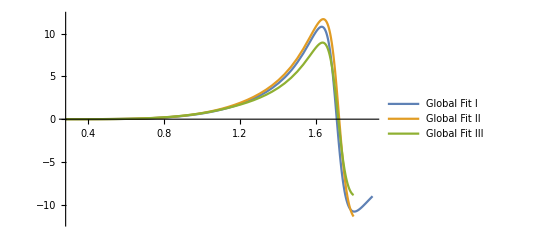

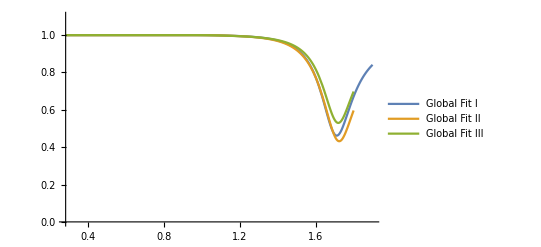

```mathematica
Plot[{δ13[e^2]/.Fpar1/.physval,ConditionalExpression[δ13[e^2]/.Fpar2/.physval,e<1.8],ConditionalExpression[δ13[e^2]/.Fpar3/.physval,e<1.8]},{e,0.28,1.9},PlotRange->{-12,12},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[{η13[e^2]/.Fpar1/.physval,ConditionalExpression[η13[e^2]/.Fpar2/.physval,e<1.8],ConditionalExpression[η13[e^2]/.Fpar3/.physval,e<1.8]},{e,0.28,1.9},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## G0 wave

#### Common parameters for the three Global Fits

#### Amplitude

First, the Breit-Wigner amplitude, valid above 1.4 GeV

```mathematica
G0par={Γf4->0.206,mf4->2.011,Rf4->4.671,xf4->0.16};
ΔG0par={ΔΓf4->0.080,Δmf4->0.023,ΔRf4->0,Δxf4->0.03};
```

```mathematica
q04=kp[mf4^2];
α04=0.5;
s004=1.75^2;
sm04=1.4^2;
sη04=1.05^2;
```

```mathematica
w04[s_]=(√s-α04 √(s004-s))/(√s+α04 √(s004-s));
v04[s_]=w04[s+ 10^-18 I];
Blatt4[s_]=s^8+10 s^6+135 s^4+1575 s^2+11025;
```

```mathematica
Γ04[s_]=Γf4 (kp[s]/q04)^9 Blatt4[q04 Rf4]/Blatt4[kp[s] Rf4];
```

```mathematica
tbw04[s_]=(xf4 mf4 Γ04[s])/(σpp[s] (mf4^2-s-I mf4 Γ04[s]));
```

```mathematica
Sbw04[s_]=1+2 I σpp[s] tbw04[s];
```

```mathematica
δbw04[s_]=Re[ArcTan[Re[Sbw04[s]],Im[Sbw04[s]]] 90/π];
```

```mathematica
ηbw04[s_]=Abs[Sbw04[s]];
```

Now, let’s define the low-energy conformal amplitude, matched to the B-W amplitude at 1.4 GeV

```mathematica
fac04[s_]=(√s)/(2 kp[s]^9)Mp^8;
```

```mathematica
cotbweff04[s_]=1/(Tan[(δbw04[s] π)/180] fac04[s]);
```

```mathematica
derc04=(cotbweff04[sm04+10^-5]-cotbweff04[sm04-10^-5])/(2 10^-5);
derv04=(v04[sm04+10^-5]-v04[sm04-10^-5])/(2 10^-5);
```

```mathematica
b104=derc04/derv04;
b004=cotbweff04[sm04]-b104 v04[sm04];
```

The conformal phase-shift is defined as

```mathematica
cotδlow04[s_]=(b004+b104 v04[s])/(σpp[s] kp[s]^8)Mp^8;
```

```mathematica
δlow04[s_]=Re[ArcCot[cotδlow04[s]] 180/π];
```

The phase-shift in the whole range is

```mathematica
δ04[s_]=Piecewise[{{δlow04[s],s<=sm04},{δbw04[s],s>sm04}}];
```

```mathematica
ϵ04=(1-ηbw04[sm04])/(1-sη04/sm04)^(9/2);
```

```mathematica
derη04=(ηbw04[sm04+10^-5]-ηbw04[sm04-10^-5])/(2 10^-5);
```

```mathematica
r04=-((sm04 derη04)/(1-ηbw04[sm04])+(7 sη04)/(2 (sm04-sη04)));
```

The elasticity in the whole range is

```mathematica
η04[s_]=Piecewise[{{1,s<=sη04},{1-Re[ϵ04] (1-sη04/s)^(9/2) (1+Re[r04] (1-sm04/s)),sη04<s<=sm04},{Re[ηbw04[s]],s>sm04}}];
```

This is the final F Global Fit parametrization

```mathematica
t04[s_]=(η04[s]Exp[ⅈ δ04[s] π/90]-1)/(2ⅈ σpp[s]);
```

#### Plots

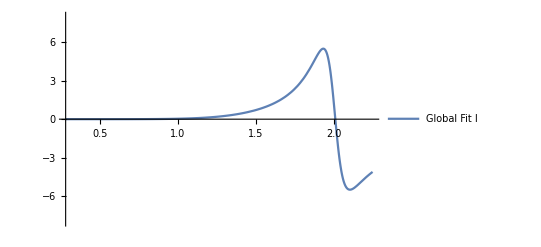

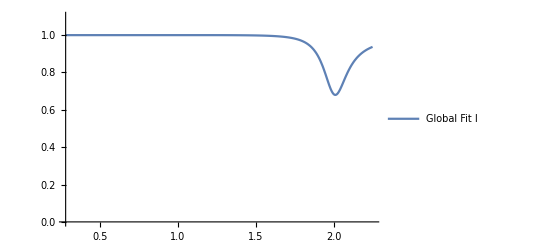

```mathematica
Plot[δ04[e^2]/.G0par/.physval,{e,0.28,2.25},PlotRange->{-8,8},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
Plot[η04[e^2]/.G0par/.physval,{e,0.28,2.25},PlotRange->{0,1.1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```

## G2 wave

#### Parameters

```mathematica
G2par1={B024->-4.57*10^6,B124->-62.15*10^6,B224->-77.05*10^6,Bh224->188*10^6,Bh324->86*10^6,Δ24->0.329};

ΔG2par1={ΔB024->0.09*10^6,ΔB124->0.13*10^6,ΔB224->0.19*10^6,ΔBh224->10*10^6,ΔBh324->21*10^6,ΔΔ24->0.023};

G2par2={B024->-4.56*10^6,B124->-62.18*10^6,B224->-76.98*10^6,Bh224->187*10^6,Bh324->110*10^6,Δ24->0.340};

ΔG2par2={ΔB024->0.09*10^6,ΔB124->0.13*10^6,ΔB224->0.19*10^6,ΔBh224->10*10^6,ΔBh324->21*10^6,ΔΔ24->0.023};

G2par3={B024->-4.57*10^6,B124->-62.11*10^6,B224->-77.00*10^6,Bh224->194*10^6,Bh324->120*10^6,Δ24->0.319};

ΔG2par3={ΔB024->0.09*10^6,ΔB124->0.13*10^6,ΔB224->0.19*10^6,ΔBh224->10*10^6,ΔBh324->21*10^6,ΔΔ24->0.023};
```

#### Amplitude

We define the phase-shift, which has two conformal pieces

```mathematica
s024=1.65^2;
sh24=2.4^2;
sm24=0.85^2;
```

```mathematica
v24[s_]=w[s+ I 10^-18,s024];
vh24[s_]=w[s+ I 10^-18,sh24];
```

```mathematica
cotδ24conf1[s_]=(s^(1/2) s Mp^8)/(2 kp[s]^9 (4*(Mp^2+ Δ24^2)-s))(B024+B124 v24[s]+B224 v24[s]^2);
```

```mathematica
Bh024=B024+B124 v24[sm24]+B224 v24[sm24]^2;
Bh124=(B124+2 B224 v24[sm24])s024/sh24 (√(sh24-sm24))/(√(s024-sm24))((√sm24+√(sh24-sm24))/(√sm24+√(s024-sm24)))^2;
```

```mathematica
cotδ24conf2[s_]=(s^(1/2) s Mp^8)/(2 kp[s]^9 (4*(Mp^2+ Δ24^2)-s))(Bh024+Bh124 (vh24[s]-vh24[sm24])+Bh224 (vh24[s]-vh24[sm24])^2+Bh324 (vh24[s]-vh24[sm24])^3);
```

The phase-shift is given by

```mathematica
δ24conf1[s_]=ArcCot[cotδ24conf1[s]];
```

```mathematica
δ24conf2[s_]=ArcCot[cotδ24conf2[s]];
```

```mathematica
δ24[s_]=Piecewise[{{δ24conf1[s],s<=sm24},{δ24conf2[s],s>sm24}}]*180/π;
```

This is the final G2 Global Fit parametrization

```mathematica
t24[s_]=(Exp[2ⅈ δ24[s]*π/180]-1)/(2ⅈ σpp[s]);
```

#### Plots

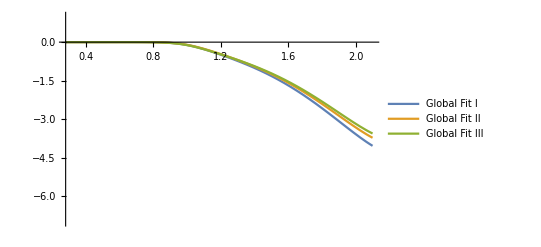

```mathematica
Plot[{δ24[e^2]/.G2par1/.physval,δ24[e^2]/.G2par2/.physval,δ24[e^2]/.G2par3/.physval},{e,0.28,2.1},PlotRange->{-7,1},PlotLegends->{"Global Fit I","Global Fit II","Global Fit III"}]
```